# Visualizing Data

```mathematica
{1,4,9,16,25}
```

{1,4,9,16,25}

```mathematica
data = %
```

{1,4,9,16,25}

```mathematica
data
```

{1,4,9,16,25}

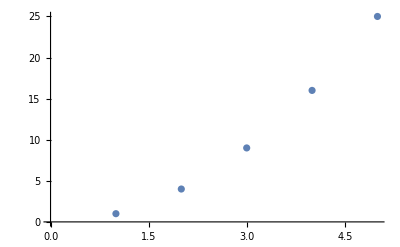

```mathematica
ListPlot[data]
```

WolframAlphaQueryParseResults

-Graphics-

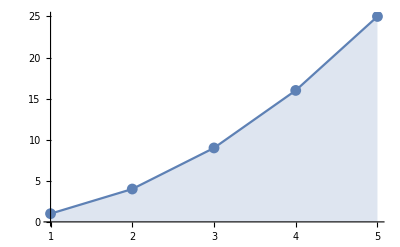

```mathematica
ListLinePlot[data, Mesh->All,
Filling->Axis,
AxesOrigin->{1,0}]
```

```mathematica
Manipulate[
lplot[data],
{lplot, {ListPlot,ListLinePlot,ListLogPlot,ListLogLogPlot}},
Initialization:>(data)]
```

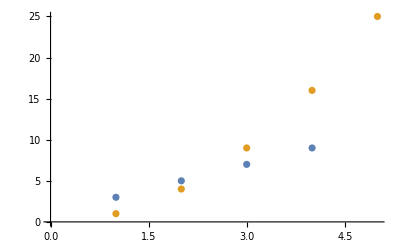

```mathematica
ListPlot[{{3,5,7,9},{1,4,9,16,25}}]
```

```mathematica
dataset1 = {1,4,9,16,25}
```

{1,4,9,16,25}

```mathematica
dataset2 = {3,5,7,8}
dataset3 = {2,5,9,14,20}
```

{3,5,7,8}

{2,5,9,14,20}

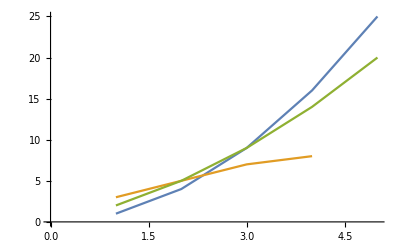

```mathematica
ListLinePlot[{dataset1,dataset2,dataset3}]
```

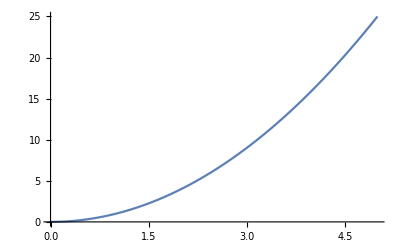

```mathematica
Plot[x^2,{x,0,5}]
```

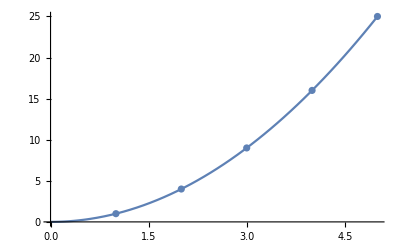

```mathematica
Show[Plot[x^2,{x,0,5}],ListPlot[{1,4,9,16,25}]]
```

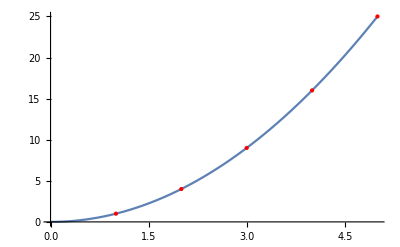

```mathematica
Show[Plot[x^2,{x,0,5}],ListPlot[{1,4,9,16,25},
PlotStyle->{Red,PointSize[Medium]}]]
```